## Basics

Mathematica has a notebook format, meaning you can have lines of code and lines of formatted text all in the same document. To create a line of code, click the + icon and select “Wolfram Language Input”. For text, click + and select either “Plain text” or “Other styles of text...” where you can choose formats like title, section, and subsection. 
Let’s execute our first command in Mathematica. We can do basic addition, subtraction, multiplication, etc. by typing the expression in a “Wolfram Language Input” environment and hitting SHIFT+ENTER:

```mathematica
2+2
```

4

We can assign a fixed value to a variable using an equals sign and suppress the output with a semicolon. This is useful when you are running lots of code at once and don’t want to see the output from each line. There is no special command to print the value of a variable in Mathematica, just type the name of the variable and execute that line of code.

```mathematica
a = 2*3;
```

```mathematica
a
```

6

Mathematica makes it super easy to visualize complicated mathematical expressions with commands that have your code read like standard math notation. We can also type ESC[...]ESC to insert special characters like π.  We can also take the help of the “Basic Math Assistant” to help with write symbolic math expressions. Go to Palettes > Basic Math Assistant.

```mathematica
√(2/3+π^4)
```

√(2/3+π^4)

To get back a numerical value instead of the algebraic expression, we will need to use the command N[ ] (note that functions in Mathematica use square brackets instead of parentheses).

```mathematica
N[√(2/3+π^4)]
```

9.90332

```mathematica
We can also do some matrix algebra!
```

```mathematica
Mat = RandomInteger[{-1, 1}, {4, 4}]
MatrixForm[Mat]
Det[Mat]
```

{{-1,0,-1,0},{1,0,0,-1},{1,0,1,1},{1,0,1,1}}

(-1 | 0 | -1 | 0
1 | 0 | 0 | -1
1 | 0 | 1 | 1
1 | 0 | 1 | 1)

0

We can do more complicated math too like derivatives and integrals. Mathematica can do a lot of arithmetic, algebra, and calculus that will save an enormous amount of time on your physics problem sets.

```mathematica
D[E^Sin[x] √x,{x,2}]
```

-ⅇ^Sin[x]/(4 x^(3/2))+(ⅇ^Sin[x] Cos[x])/(√x)+√x (ⅇ^Sin[x] Cos[x]^2-ⅇ^Sin[x] Sin[x])

Another way to do this is to define mathematical functions and simply ask for the derivative of that function. Be careful to use := for delayed assignment so that your function will evaluate at the argument you input each time you use the function. The notation x_ tells Mathematica to match a pattern. There are more complex usages of this notation, but in this case it will substitute the entire argument of the function everywhere x appears.

```mathematica
f[x_]:=E^Sin[x] √x;
g[x_]:=D[f[x],{x,2}];
g[x]
```

-ⅇ^Sin[x]/(4 x^(3/2))+(ⅇ^Sin[x] Cos[x])/(√x)+√x (ⅇ^Sin[x] Cos[x]^2-ⅇ^Sin[x] Sin[x])

We can do integrals too! (make sure to clear variables before reusing them)

```mathematica
Clear[a]
∫_0^∞ E^(-a x^2)ⅆx
```

ConditionalExpression[(√π)/(2 √a), Re[a]>0]

You can use Wolfram Alpha to show you the step-by-step procedure of solving the integral

```mathematica
WolframAlpha["int E^(-ax^2) over x",PodStates->{"Step-by-step solution"}]
```

WolframAlphaQueryResults

Another cool feature is that Mathematica has access to the entire database of Wolfram Alpha, so we can enter free-form input using CTRL= to get this data from the internet and perform calculations.

```mathematica
(* this gives us the time it takes a cheetah to run across the sun at max speed*)
x = (Entity["Star","Sun"][EntityProperty["Star","Diameter"]])/(Entity["Species","Species:AcinonyxJubatus"][EntityProperty["Species","MaximumSpeed"]])
```

11527.8 h

One last feature we’ll go over is Tables. Tables allow you to generate lists of data points, algebraic expressions, and more in a single line of code. Here we’ll list the first through fifth derivatives of our function f[x] defined earlier evaluated at the point x=1.

```mathematica
Clear[x]
A = Table[Simplify[D[f[x],{x,i}]],{i,1,5}]
x=1;
N[A]
```

{(ⅇ^Sin[x] (1+2 x Cos[x]))/(2 √x),(ⅇ^Sin[x] (-1+4 x Cos[x]+4 x^2 Cos[x]^2-4 x^2 Sin[x]))/(4 x^(3/2)),(ⅇ^Sin[x] (3+12 x^2 Cos[x]^2+8 x^3 Cos[x]^3-12 x^2 Sin[x]-2 x Cos[x] (3+4 x^2+12 x^2 Sin[x])))/(8 x^(5/2)),-1/(16 x^(7/2))ⅇ^Sin[x] (15+12 x^2+2 x^4+8 x (-3+x^2) Cos[x]+12 (x^2+4 x^4) Cos[2 x]-8 x^3 Cos[3 x]-2 x^4 Cos[4 x]-24 x^2 Sin[x]+8 x^4 Sin[x]+48 x^3 Sin[2 x]+24 x^4 Sin[3 x]),1/(32 x^(9/2))ⅇ^Sin[x] (105+60 x^2-10 x^4-2 x (75-10 x^2+34 x^4) Cos[x]-60 x^2 (-1+4 x^2) Cos[2 x]-20 x^3 Cos[3 x]-190 x^5 Cos[3 x]+10 x^4 Cos[4 x]+2 x^5 Cos[5 x]-120 x^2 Sin[x]-40 x^4 Sin[x]+120 x^3 Sin[2 x]+160 x^5 Sin[2 x]-120 x^4 Sin[3 x]-40 x^5 Sin[4 x])}

{2.41327,-0.601384,-6.03389,-5.53603,33.2135}

We can easily plot the content of a list using ListPlot.

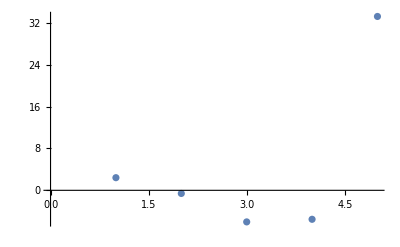

```mathematica
ListPlot[A]
```

## Physics

Now let’s do some actual physics. As an example problem, we’re going to think about gravity and see how we can use Mathematica to visualize and calculate. Let’s start by generating a 3D plot of the gravitational potential generated by a point mass at the origin.
First we’ll need the numerical values of the relevant constants.

```mathematica
(*Newton's gravitational constant in m^3 kg^-1 s^-2 *)
G = 6.674*10^-11;
(* mass of the point mass in kg *)
M = 1;
```

We generate our plot using Plot3D and inputting the function to plot, ranges for the variables, and specifying options like axes labels and a label for the plot (don’t worry if you don’t know where this equation comes from!).

```mathematica
Plot3D[(-G M)/(√(x^2+y^2)),{x,-10,10},{y,-10,10},PlotRange-> Automatic,PlotLabel->"Gravitational Potential",AxesLabel->{"x","y","ϕ(x,y)"}]
```

-Graphics3D-

Next we’ll think about trajectories in gravity with air resistance. Our goal will be to visualize how a trajectory will change with increasing levels of air resistance. We’ll need to use Newton’s second law, which will take the form mx’’[t]== -mg-α x’[t] for a downward force of gravity and an additional force from air resistance with a strength set by the constant α. This differential equation is difficult to solve, so instead let’s have Mathematica solve it for us using NDSolve[ ]. Note that we have to provide sufficient initial conditions like the initial height and speed for NDSolve to be able to solve a differential equation numerically like this.

```mathematica
Clear[x]
m = 1;
g = 9.8;
α = 3;
?NDSolve
sol = NDSolve[{m x''[t]== -m g-α x'[t],x[0]==0,x'[0]==5},x[t],{t,0,1}]
```

{{x[t]→InterpolatingFunction[…][t]}}

```mathematica
x[t]/.sol
```

{InterpolatingFunction[…][t]}

We can plot the result using Plot[ ]. Plotting interpolating functions like this comes with strange notation that you don’t have to worry about. Just know that the Plot[ ] function has 2 inputs: the first is the function to plot, and the second specifies the domain.

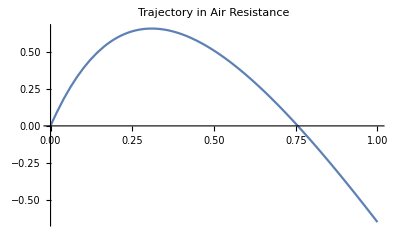

```mathematica
Plot[x[t]/.sol,{t,0,1}, PlotLabel->"Trajectory in Air Resistance"]
```

We can see that the object reaches a terminal velocity on its way down, just as we would expect! 
Now we want to compare what the trajectory looks like with different values for the strength of air resistance. To visualize this, let’s first generate a list of interpolating functions using Table[ ] and NDSolve[ ].

```mathematica
Clear[sol]
Clear[α]
sol = Table[NDSolve[{m x''[t]== -m g-α x'[t],x[0]==0,x'[0]==5},x[t],{t,0,10}],{α,0,20,0.1}];
```

Finally, let’s create an animation of the results using Animate[ ]. Notice that the required inputs for Animate[ ] are very similar to those for Table[ ].

```mathematica
Animate[Plot[x[t]/.sol[[i]],{t,0,1},PlotRange->{0,1.5},PlotLabel->"Trajectory x[t]"],{i,1,200,1}]
```

We can pause, speed up, slow down, and scroll through the animation using the controls on the right.
That’s it for now in Mathematica! Next we’ll use LaTex to write a report on our results with math typesetting and standard scientific formatting. Leave this window open so we can come back and export some of the figures we generated.